This Mathematica notebook contains the code to produce the supplemental figures for “Fertilization by coral-dwelling fish promotes coral growth but can exacerbate bleaching response” by A.R. Detmer, R. Cunning, F. Pfab, A.L. Brown, A. C. Stier, R.M. Nisbet, and H.V. Moeller.

## Define constant parameters (run this first)

```mathematica
(* list of parameters and expressions that don't change, run this before running any of the other code*)
(*values that were varied in the model simulations are commented out here*)
(*parameters from original Cunning et al. 2017 model (see Table 2 of Cunning et al. 2017)*)
nNH=.18;(*N:C molar ratio in host biomass*)
nNS=.13; (*N:C molar ratio in symbiont biomass*)
nNX=.2; (*N:C molar ratio in prey biomass*)
j0HT=.03;(*maintenance rate of host biomass*)
j0ST=.03;(*maintenance rate of symbiont biomass*)
σNH=.9;(*proportion of N turnover recycled in host*)
σCH=.1;(*proportion host metabolic CO2 recycled to photosynthesis*)
σNS=.9;(*proportion of N turnover recycled in symbiont*)
σCS=.9;(*proportion symbiont metabolic CO2 recycled to photosynthesis*)
jXm=.13;(*maximum prey assimilation rate from host feeding*)
KX=10^-6;(*half-saturation constant for prey assimilation*)
jNm=.035; (*maximum host DIN uptake rate*)
KN=1.5*10^-6; (* half-saturation constant for host DIN uptake*)
kCO2=10; (*efficacy of CO2 delivery to photosynthesis by host carbon concentrating mechanisms*)
jHGm=1;(*maximum specific growth rate of host*)
yCL=.1; (*quantum yield of photosynthesis*)
yC=.8; (*yield of biomass formation from carbon*)
astar=1.34; (*effective light-absorbing cross-section of symbiont*)
kNPQ=112; (* non-photochemical quenching (NPQ) capacity of symbiont*)
kROS=80; (* excess photon energy that doubles ROS production relative to baseline levels *)
jCPm=2.8; (*maximum specific photosynthesis rate of symbiont*)
jSGm=0.25;(*maximum specific growth rate of symbiont*)
b=5;(*scaling parameter for bleaching response*)
(*X=0;*)(*concentration of prey in environment*)
(*Ν=1*10^-7;*)(* ambient concetration of nitrogen in external environment*)
L=15; (* external light*)
λ=50; (* Pfab et al. (submitted)'s lambda parameter for simulating fluxes as ODEs (continuous time approximation method for simulating the system) *)

(* parameters for host volume*)
kv=16.9; (* liters per C-mol H*)
γ= 1; (*scales H biomass to volume *)
vi=0.7; (* fraction of coral volume occupied by water; based on Zawada et al. P. damicornis data; see supplement for details *)

(* parameters for fish*)
kp=210;(*scales fish carrying capacity with biomass of host, calculated using kv=16.9 C-mol/L*)
rp=0.05; (* intrinsic growth rate*)
Bp = 1; (* intraspecific competition coefficient*)
ep=1.5*10^-5; (* damselfish excretion rate (total mols N per g per d); calculated using data on D. flavicaudus*)

(* parameters for nitrogen equations*)
α = 0.23; (* proportion of coral tissue in direct contact with the external environment*)

d=1660; (*flushing rate, units of 1/days*)
ζ =1; (* fraction of waste N released by the symbiont that is bioavailable to the coral*)

(* derived parameters*)
(*jX=(jXm X)/(X+KX);*)(* prey uptake from environment*)
(* jN=(jNm Ν)/(Ν+KN);*) (* N uptake from environment*)
jHT=j0HT; (*rate of host biomass turnover*)
rNS=σNS nNS j0ST;(*nitrogen recycled from symbiont biomass turnover*)


(* initial conditions*)
H0=1; (*intial host biomass*)
S0=0.3; (*initial symbiont biomass*)
jCP0=1;
ρC0= 1; 
(*healthy state: jCP0 and ρC=jCPm or 1, bleached state: jCP0 and ρC=0 *)
VH0=kv*H0^γ; (*initial host volume*)
(*Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)
(*jNw0= (jNm*Ν)/(Ν+KN)*H0/S0;*)
(*P0=0;*)(*kp*(1-α)*H0*)(*change P0 depending on whether or not fish are present*)


(*function to remove identifiers from simulations run in Module[]*)
str[expr_]:=Module[{},StringReplace[ToString[expr,FormatType->StandardForm],c:WordCharacter~~"$"~~DigitCharacter..:>c]];
```

## Fig. S1: Bifurcation diagrams of waste N and fish excretions as a function of prey availability

### Run simulations and format results

#### check that steady state is reached

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 

X2BifurRuns1= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,maketmax, steadyNi,steadyHGrowth,steadySH,steadyjNw,steadyep(*make sure to put any intermediate output values in Module*)},
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni over the last 50 days of the simulation*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];


{steadyNi,steadyHGrowth,steadySH}(*record the changes in Ni, H growth, and S/H values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}(*different levels of prey*)
];
```

```mathematica
Select[Flatten[X2BifurRuns1], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 


X2BifurRuns= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,maketmax, steadyNi,steadyHGrowth,steadySH,steadyjNw,steadyep(*make sure to put any intermediate output values in Module*)},
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

(*symbiont waste nitrogen*)
(*need to add tmax to the state variables involved in the calculation of jNw (S and VH need to be changed to S[t] and VH[t])*)
maketmax=((#->#[tmax])&/@states);
steadyjNw=Evaluate@Flatten@{(ζ*(1-α)*jNw*S)/( vi*VH)/.maketmax/.sol};

(*fish excretion*)
steadyep=Evaluate[{(ep*P[tmax])/( vi*VH[tmax])}/.sol];

{steadyNi,steadyHGrowth,steadySH,steadyjNw,steadyep}(*the steady state values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}(*different levels of prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["SXBifur",X2BifurRuns]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["SXBifur"];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (have 2 (fish/no fish) for each of the 5 outputs, so 10 lists total*)

(*transpose this to change the nested list from {{P1 at X1, P2 at X1}, {X2}, ...{Xn}} to {{X1, X2, ... Xn at P1}, {P2}} *)
XseparatePX=Transpose[X2BifurRuns];
(*prey no fish*)
XBifurNoPX=XseparatePX[[1]];
separateXNoPX=Transpose[XBifurNoPX];(*group each output together*)
XBifurNoPXNi=separateXNoPX[[1]];(*Ni values at each prey level for no fish*)
XBifurNoPXgrowth=separateXNoPX[[2]];(*dH/Hdt values at each prey level for no fish*)
XBifurNoPXSH=separateXNoPX[[3]];(*S/H values at each prey level for no fish *)
(*symbiont excretion values at each prey level for no fish, need to flatten out the list of values*)
XBifurNoPXjNw=Flatten[separateXNoPX[[4]]];
(*fish excretion values at each prey level for no fish, need to flatten out the list of values*)
XBifurNoPXep=Flatten[separateXNoPX[[5]]];

(* prey with fish*)
XBifurPX=XseparatePX[[2]];
separateXPX=Transpose[XBifurPX];(*group each output together*)
XBifurPXNi=separateXPX[[1]];(*Ni values at each prey level with fish*)
XBifurPXgrowth=separateXPX[[2]];(*dH/Hdt values at each prey level with fish*)
XBifurPXSH=separateXPX[[3]];(*S/H values at each prey level with fish*)
(*symbiont excretion values at each prey level with fish*)
XBifurPXjNw=Flatten[separateXPX[[4]]];
(*fish excretion values at each prey level with fish*)
XBifurPXep=Flatten[separateXPX[[5]]];

(*list of X values*)
XVals={0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7};
(*to add Nenv to the plots*)
Ν=1*10^-7;
XNenvVal=ConstantArray[Ν,Length[XVals]];
XBifurNenvLine=Transpose@{XVals,XNenvVal};

(*make list of the no prey values to plot as reference lines*)
noXnoPNiList=ConstantArray[XBifurNoPXNi[[1]],Length[XVals]];
noXPNiList=ConstantArray[XBifurPXNi[[1]],Length[XVals]];
noXnoPgrowthList=ConstantArray[XBifurNoPXgrowth[[1]],Length[XVals]];
noXPgrowthList=ConstantArray[XBifurPXgrowth[[1]],Length[XVals]];
noXnoPSHList=ConstantArray[XBifurNoPXSH[[1]],Length[XVals]];
noXPSHList=ConstantArray[XBifurPXSH[[1]],Length[XVals]];
noXnoPjNwList=ConstantArray[XBifurNoPXjNw[[1]],Length[XVals]];
noXPjNwList=ConstantArray[XBifurPXjNw[[1]],Length[XVals]];
noXnoPepList=Flatten[ConstantArray[XBifurNoPXep[[1]],Length[XVals]]];
noXPepList=Flatten[ConstantArray[XBifurPXep[[1]],Length[XVals]]];

(*use Table to get the lists in the form to plot*)
XBifurLists=Table[Module[{PlotList},PlotList=Transpose@{XVals,list}; PlotList], {list, {noXnoPNiList,noXPNiList,XBifurNoPXNi,XBifurPXNi,noXnoPgrowthList,noXPgrowthList,XBifurNoPXgrowth,XBifurPXgrowth,(*noXnoPSHList,noXPSHList,XBifurNoPXSH,XBifurPXSH,*)noXnoPjNwList,noXPjNwList,XBifurNoPXjNw,XBifurPXjNw,noXnoPepList,noXPepList,XBifurNoPXep,XBifurPXep}}];
```

### Plot the results

```mathematica
(*padding for the plot margins*)
paddingS1={{80(*left*),15(*right*)}, {50(*bottom*),10(*top*)}};
(*Ni vs prey*)
plotS1a=ListLinePlot[{XBifurLists[[1]], XBifurLists[[2]],XBifurLists[[3]], XBifurLists[[4]],XBifurNenvLine},
Epilog->Text[Style["a) Interstitial nitrogen",{Black,14}],Offset[{5(*right from top left*),-5.5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS1,PlotRange->{Full,{0, 1.4*10^-7}}(*Full*),PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[GrayLevel[0.73](*, Thin*)]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{4*10^-8, "4*10^-8"},{8*10^-8, "8*10^-8"},{1.2*10^-7, "1.2*10^-7"}},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{"mol N L^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1/GoldenRatio];

(*dH/Hdt vs prey*)
plotS1b=ListLinePlot[{XBifurLists[[5]], XBifurLists[[6]],XBifurLists[[7]], XBifurLists[[8]]},Epilog->Text[Style["b) Host specific growth rate",{Black,14}],Offset[{5(*right from top left*),-6.5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS1,PlotRange->{Full, {0, 0.028}},PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{"C-mol H C-mol H^-1 d^-1 ",None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1/GoldenRatio];

(*symbiont waste N vs. prey*)
plotS1c=ListLinePlot[{XBifurLists[[9]], XBifurLists[[10]],XBifurLists[[11]], XBifurLists[[12]]},Epilog->Text[Style["c) Waste nitrogen per volume",{Black,14}],Offset[{5(*right from top left*),-6(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS1,PlotRange->{Full,{0, 3.5*10^-5}}(*Full*),PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[Black, Thin]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{1*10^-5, "1*10^-5"},{2*10^-5, "2*10^-5"},{3*10^-5, "3*10^-7"}},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{"mol N L^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1/GoldenRatio];

(*fish excretions vs. prey*)
plotS1d= ListLinePlot[{XBifurLists[[13]], XBifurLists[[14]],XBifurLists[[15]], XBifurLists[[16]]},Epilog->Text[Style["d) Fish excretions per volume",{Black,14}],Offset[{5(*right from top left*),-5.5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS1,PlotRange->{Full,{0, 0.0002}}(*Full*),PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[Black, Thin]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0.00005, 0.0001, 0.00015},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{"mol N L^-1 d^-1",None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1/GoldenRatio];
```

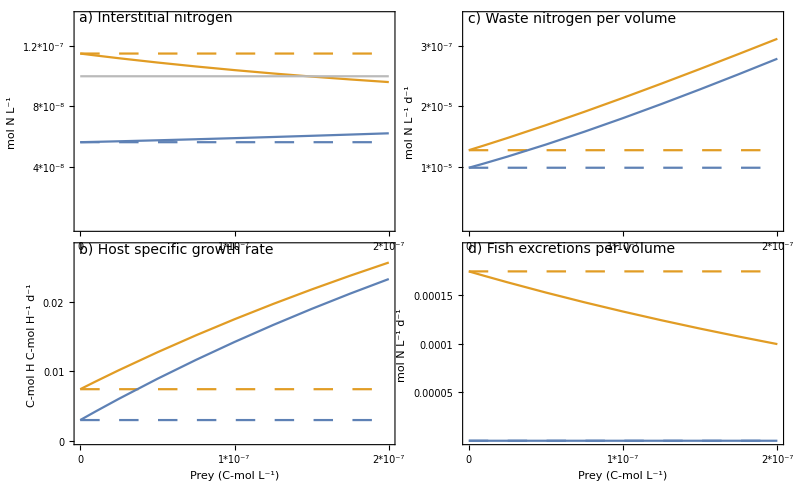

```mathematica
(*make the plot legend*)
BifurLeg=LineLegend[{ColorData[97,"ColorList"][[1]],{ColorData[97,"ColorList"][[1]],Dashing[Large]},  ColorData[97,"ColorList"][[2]],{ColorData[97,"ColorList"][[2]],Dashing[Large]}}, {"No fish, with prey","No fish, no prey","With fish, with prey","With fish, no prey"}, LegendLayout->{"Row",1},LabelStyle->Directive[FontSize->14]];

(*make the figure*)
SBifurFig=Show[Legended[GraphicsGrid[{{plotS1a, plotS1c},{plotS1b, plotS1d}}, ImageSize->Full,(*Spacings->{ 0(*left to right*),-20(*Scaled[0.1]*)(*top to bottom*)}*)Spacings->{ {0(*left?*),-20 (*labels and left col*)(*left to right*)},{0(*top?*),-20(*middle 2 rows*) (*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom (*align the grid at the bottom of its frame*)],Placed[BifurLeg,(*Bottom*){Center(*left to right position is in the center*), 0(*top to bottom position*)}]], Graphics[Text["N_i = N_env",{80 (*more pos=farther right*),-54(*more neg=further down*)}]]]
```

## Fig. S2: Bifurcation heat maps

### Run simulations and format results

#### Check steady state for Nenv vs prey simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=1500; 

NXRunsTest=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},


F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];
{steadyNi,steadyHGrowth,steadySH}(*record the changes in Ni, H growth, and S/H as output*)],

{X, {0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}],(*repeat all this for different levels of prey*)
{Ν,{0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,2.5*10^-7,5*10^-7,7.5*10^-7,10*10^-7}}(*repeat all this for different Nenv values*)
],
{P0, {0, kp*(1-α)*H0}}(*run everything once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
];
```

```mathematica
Select[Flatten[NXRunsTest], #>1*10^-4&] (*see whether any outputs are greater than 10^-4*)
(*no fish case: some simulations did not reach the steady state (changes were greater than 10^-4)*)
Select[Flatten[NXRunsTest[[1]]], #>1*10^-4&]
(*with fish case: all simulations reached the steady state*)
Select[Flatten[NXRunsTest[[2]]], #>1*10^-4&]
```

{0.000826753,0.000233035,0.00259319,0.00120395,0.00077321,0.00492071,0.00405663,0.00545449,0.000112131,0.00500471,0.0158111,0.002002,0.0439383}

{0.000826753,0.000233035,0.00259319,0.00120395,0.00077321,0.00492071,0.00405663,0.00545449,0.000112131,0.00500471,0.0158111,0.002002,0.0439383}

{}

```mathematica
(*check to see which simulations did not reach the steady state*)
(*host growth*)
NXgrowthnoPdiff=Transpose[Flatten[NXRunsTest[[1]], 1]][[2]];
(*Ni*)
NXNinoPdiff=Transpose[Flatten[NXRunsTest[[1]], 1]][[1]];

(*put the results in matrix form*)
MatrixNXnoPgrowth=ArrayReshape[NXgrowthnoPdiff, {9, 10}] ;
MatrixNXnoPNi=ArrayReshape[NXNinoPdiff, {9, 10}] ;

(*check which positions of these matrices had changes greater than 10^-4*)
Position[MatrixNXnoPgrowth,_?(#>1*10^-4&)]
Position[MatrixNXnoPNi,_?(#>1*10^-4&)]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}

{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}

There are 6 cases where the steady state is not reached: at positions 1, 2, and 3 of the first column (corresponding to the 3 lowest values of Nenv with 0 prey), at positions 1 and 2 of the second column (corresponding to the 2 lowest values of Nenv with prey=0.1*10^-7, and at position 2 of the third column (corresponding to the lowest value of Nenv with prey=0.25*10^-7).  All of these different situations are run individually in the following code chunks.

1. NO PREY, Nenv= 0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=2500; 

NXnoXlowestN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is asymptotically approaching 0, so if it is less than 10^-10 at the end of the time step say that the percent change is equal to zero*)

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXnoXlowestN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

2. NO PREY, Nenv= 0.25*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=2.5*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=5000; 

NXnoXsecLowN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},


F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L (*Lfun9*);
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step say that the percent change is equal to zero*)

(*percent change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXnoXsecLowN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

3. NO PREY, Nenv=0.5*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=5*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=50000; 

NXnoXlowestN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step say that the percent change is equal to zero*)

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXnoXlowestN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

4. PREY=0.1*10^-7, Nenv=0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=1*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=5000; 

NXlowestXlowestN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step (asymptotically approaching 0), say that the percent change is equal to zero*)

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXlowestXlowestN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

5. PREY=0.1*10^-7, Nenv=2.5*10^-8

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660(*10*);
Ν=2.5*10^-8 (*1*10^-6*);

X=1*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=50000; 

NXlowestXseclowestN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step say that the percent change is equal to zero*)

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXlowestXseclowestN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

6. PREY=2.5*10^-8, Nenv=0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=2.5*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=250000; 

NXseclowestXlowestN=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step say that the percent change is equal to zero*)

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the change in Ni, H growth, and S/H as output*)];
```

```mathematica
Select[Flatten[NXseclowestXlowestN], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

#### Simulations for Nenv vs. prey

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
d=1660;
Ν=1*10^-7 (*1*10^-6*);

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=1500; 

NXRuns=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},


F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)],

{X, {0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}],(*repeat this for different levels of prey*)
{Ν,{0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,2.5*10^-7,5*10^-7,7.5*10^-7,10*10^-7}}(*repeat this for different values of Nenv*)
],
{P0, {0, kp*(1-α)*H0}}(*repeat this with no fish (P0=0) and with fish (P0=kp*(1-α)*H0)*)
];
```

```mathematica
(*saving the output of Table[]*)
(*Save["NRunsnoPnoX1",durationRunsnoPnoX1 ]*)
Save["NXRuns",NXRuns ]
```

```mathematica
(*recover this output*)
Get["NXRuns" ];
```

Repeat this for the situations in which the system has not reached the steady state by tmax=1500:
1. NO PREY, Nenv= 0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=2500; 

NXnoXlowestN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["noXlowestN2",NXnoXlowestN2]
```

2. NO PREY, Nenv= 0.25*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=2.5*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=5000; 

NXnoXsecLowN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["noXsecLowN2",NXnoXsecLowN2]
```

3. NO PREY, Nenv=0.5*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660(*10*);
Ν=5*10^-8 (*1*10^-6*);

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=50000; 

NXnoXthirdLowN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["noXthirdLowN2",NXnoXthirdLowN2]
```

4. PREY=0.1*10^-7, Nenv=0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=1*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=5000; 

NXlowestXlowestN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["lowestXlowestN2",NXlowestXlowestN2]
```

5. PREY=0.1*10^-7, Nenv=2.5*10^-8

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=2.5*10^-8 ;

X=1*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=50000; 

NXlowestXseclowestN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},


F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["lowestXseclowestN2",NXlowestXseclowestN2]
```

6. PREY=2.5*10^-8, Nenv=0.1*10^-7

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-8 (*1*10^-6*);

X=2.5*10^-8;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=250000; 

NXseclowestXlowestN2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];
(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];
(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];

Save["seclowestXlowestN2",NXseclowestXlowestN2]
```

#### Get results for Nenv vs prey simulations in correct form to plot

```mathematica
Get["NXRuns" ];
Get["noXlowestN2"];
Get["noXsecLowN2"];
Get["noXthirdLowN2"];
Get["lowestXlowestN2"];
Get["lowestXseclowestN2"];
Get["seclowestXlowestN2"];
```

```mathematica
(*NXRuns is nested list, innermost is all 3 outputs for {X1, X2, ...}, second level is this repeated for each Nenv {N1, N2, ...}, outer levels is fish {P1, P2}, *)
(*so first seprate the fish vs no fish cases*)
NXnoP=NXRuns[[1]];
NXwithP=NXRuns[[2]];
separate=Transpose[Flatten[NXnoP, 1]];(* this separates all 3 response variables, but need to know that in the resulting array, the columns are the X values (outermost parameter tested) and the rows are the N levels (outermost parameter tested), so if n X values are tested, the first n values are the outputs for each X value at the first N value tested, all the way to the mth set of n outputs for the mth N value tested*)
noPNi=separate[[1]];
(*could combine the above two lines of code*)
noPNi=Transpose[Flatten[NXnoP, 1]][[1]];

(*want the differences between the P and no P case*)
(*Ni*)
MatrixNXNinoP1=ArrayReshape[Transpose[Flatten[NXnoP, 1]][[1]], {9, 10}] ;(*{n, m} dimensions are {# outermost par values, # innermost par values} *)
MatrixNXNinoP=ReplacePart[MatrixNXNinoP1,{{1,1}-> NXnoXlowestN2[[1]],{1,2}-> NXnoXsecLowN2[[1]],{1,3}-> NXnoXthirdLowN2[[1]],{2,1}-> NXlowestXlowestN2[[1]],{2,2}-> NXlowestXseclowestN2[[1]],{3,1}-> NXseclowestXlowestN2[[1]]}];(*elements {{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}} of the array for the no P case had not reached the steady state, so need to replace these with the results of the separately run simulations*)
MatrixNXNiP=ArrayReshape[Transpose[Flatten[NXwithP, 1]][[1]], {9, 10}] ;
NXNidiff=MatrixNXNiP-MatrixNXNinoP;

(*repeat for host growth rates*)
MatrixNXgrowthnoP1=ArrayReshape[Transpose[Flatten[NXnoP, 1]][[2]], {9, 10}] ;
MatrixNXgrowthnoP=MatrixNXNinoP=ReplacePart[MatrixNXgrowthnoP1,{{1,1}-> NXnoXlowestN2[[2]],{1,2}-> NXnoXsecLowN2[[2]],{1,3}-> NXnoXthirdLowN2[[2]],{2,1}-> NXlowestXlowestN2[[2]],{2,2}-> NXlowestXseclowestN2[[2]],{3,1}-> NXseclowestXlowestN2[[2]]}];
MatrixNXgrowthP=ArrayReshape[Transpose[Flatten[NXwithP, 1]][[2]], {9, 10}] ;
NXgrowthdiff=MatrixNXgrowthP-MatrixNXgrowthnoP;

(* S/H*)
MatrixNXSHnoP1=ArrayReshape[Transpose[Flatten[NXnoP, 1]][[2]], {9, 10}] ;
MatrixNXSHnoP=MatrixNXNinoP=ReplacePart[MatrixNXSHnoP1,{{1,1}-> NXnoXlowestN2[[3]],{1,2}-> NXnoXsecLowN2[[3]],{1,3}-> NXnoXthirdLowN2[[3]],{2,1}-> NXlowestXlowestN2[[3]],{2,2}-> NXlowestXseclowestN2[[3]],{3,1}-> NXseclowestXlowestN2[[3]]}];
MatrixNXSHP=ArrayReshape[Transpose[Flatten[NXwithP, 1]][[2]], {9, 10}] ;
NXSHdiff=MatrixNXSHP-MatrixNXSHnoP;
```

#### Check steady state for flushing rate vs carrying capacity simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
d=1660;
Ν=1*10^-7 (*1*10^-6*);
X=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=800; 

kdRunsTest=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(* change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the changes in Ni, H growth, and S/H as output*)],

{kp,{150,175,200,225,250,275,300,325,350,375,400}}],(*repeat for all the kp's*)
{d,{450,850,1250,1650,2050,2450,2850,3250,3650,4050}}(*repeat for all the flushing rates*)
],
{P0, {0, kp*(1-α)*H0}}(*repeat the above with no fish (P0=0) and with fish (P0=kp*(1-α)*H0)*)
];
```

```mathematica
Select[Flatten[kdRunsTest], #>1*10^-4&] (*check that nothing is greater than 10^-4*)
```

{}

#### Simulations for flushing rate vs carrying capacity

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh]
```

```mathematica
d=1660;
Ν=1*10^-7 ;
X=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=800; 

kdRuns=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*record the steady state values as output*)],

{kp,{150,175,200,225,250,275,300,325,350,375,400}}],(*repeat for the different kp's*)
{d,{450,850,1250,1650,2050,2450,2850,3250,3650,4050}}(*repeat for the different flushing rates*)
],
{P0, {0, kp*(1-α)*H0}}(*repeat with no fish (P0=0) and with fish (P0=kp*(1-α)*H0)*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["kpdRuns",kdRuns ]
```

```mathematica
(*recover this output*)
Get["kpdRuns" ];
```

#### Get results for flushing rate vs carrying capacity correct form

```mathematica
kdRuns ;(*nested list, innermost is all 3 response variables for {kp1, kp2, ...}, second level is this repeated for each flushing rate {d1, d2, ...}, outer levels is fish {P1, P2}, *)
(*so first seprate the fish vs no fish cases*)
kdnoP=kdRuns[[1]];
kdwithP=kdRuns[[2]];
(*want the differences between the P and no P case*)
(*Ni*)
kdNidiff=Transpose[Flatten[kdwithP, 1]][[1]]-Transpose[Flatten[kdnoP, 1]][[1]];
(*host growth*)
kdgrowthdiff=Transpose[Flatten[kdwithP, 1]][[2]]-Transpose[Flatten[kdnoP, 1]][[2]];
(*S/H*)
kdSHdiff=Transpose[Flatten[kdwithP, 1]][[3]]-Transpose[Flatten[kdnoP, 1]][[3]];

(*turn the results into matrices for plotting*)
MatrixkdNi=ArrayReshape[kdNidiff, {10, 11}] ;(*{n, m} dimensions are {# outermost par values, # innermost par values} *)
Matrixkdgrowth=ArrayReshape[kdgrowthdiff, {10, 11}] ;
MatrixkdSH=ArrayReshape[kdSHdiff, {10, 11}] ;
```

### Plot results

```mathematica
paddingShm={{80(*left*),15(*right*)}, {50(*bottom*),0(*top*)}};

plotShma=MatrixPlot[Reverse[NXgrowthdiff], ImageSize-> Full,(*PlotLegends->Automatic, *)ColorFunction->(ColorData[{"GrayTones",{0(*Min[MatrixNXgrowth]*),Max[NXgrowthdiff]}}]),ColorFunctionScaling->False(*need to specify the colorfunction to match the legend specified by BarLegend[], need to add colorfunctionscaling false to make the plot colors match these values*),Mesh->True, Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameLabel->{{"Prey (C-mol L^-1)",None},{"Ambient N (mol N L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12],FrameTicks->{{{{1, "10×10^-7"},{2, "7.5×10^-7"},{3, "5×10^-7"},{4, "2.5×10^-7"},{5, "1×10^-7"},{6, "0.75×10^-7"},{7, "0.5×10^-7"},{8, "0.25×10^-7"},{9, "0.1×10^-7"}}, None}, {{{1, 0},(*{2, "0.1*10^-7"},*){3, "0.25×10^-7"},(*{4, "0.5*10^-7"},*){5, "0.75×10^-7"},(*{6, "1*10^-7"},*){7, "1.25×10^-7"},(*{8, "1.5*10^-7"},*){9, "1.75×10^-7"}(*,{10, "2*10^-7"}*)}, None}},PlotLabel->"a) dH/Hdt with fish-dH/Hdt without fish",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingShm]; 

plotShmb=MatrixPlot[Reverse[Matrixkdgrowth], ColorFunction->(ColorData[{"GrayTones",{0,Max[Matrixkdgrowth]}}]),ColorFunctionScaling->False, ImageSize-> Full,Mesh->True, Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameLabel->{{"Fish:host biomass scalar (g C-mol H^-1)",None},{"Flushing rate (d^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12],FrameTicks->{{{{1, "4050"},{2, "3650"},{3, "3250"},{4, "2850"},{5, "2450"},{6, "2050"},{7, "1650"},{8, "1250"},{9, "850"},{10, "450"}}, None}, {{{1, 150},{2, 175}, {3, 200},{4, 225},{5, 250},{6, 275},{7, 300},{8, 325},{9, 350},{10, 375},{11, 400} }, None}},PlotLabel->"b) dH/Hdt with fish- dH/Hdt without fish",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingShm] ;
```

```mathematica
plotShmaLeg=BarLegend[{GrayLevel,{0(*Min[MatrixNXgrowth]*),Max[NXgrowthdiff]}}];
plotShmbLeg=BarLegend[{GrayLevel,{0,Max[Matrixkdgrowth]}}];

Legended[GraphicsGrid[{{plotShma, plotShmb}} ,ImageSize->Full,Spacings->{ {10(*left*),40 (*labels and left col*)(*left to right*)},{0(*top*),0(*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*)], {Placed[plotShmaLeg,(*Bottom*){1.425(*left to right position is in the center*), 0.5(*top to bottom position*)}], Placed[plotShmbLeg,(*Bottom*){0.5(*left to right position is in the center*),0.5(*top to bottom position*)}]}]
```

-Graphics-

## Fig. S3: Fish: host biomass at different fish growth rates

### Run the simulations and format results

#### Run simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=0;(*no prey*)
P0=kp*(1-α)*H0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=2000; 

(*use nested Table to simulate the model at different levels of nitrogen (corresponding to different steady state host growth rates) and different fish growth rates*)
PHrpRuns=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyHGrowth,steadyPH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state host growth rate*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state fish to interstitial host biomass ratio*)
steadyPH=Evaluate[P[tmax]/((1-α)*H[tmax])/.sol];

{steadyHGrowth,steadyPH}(*record the steady state host growth rate and P/H ratio as output*)],

{rp, {0.01, 0.05,0.1}}],(*repeat this for different fish growth rates*)
{Ν,{0.1*10^-7,0.5*10^-7,1*10^-7,2*10^-7,2.5*10^-7,3*10^-7,4*10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,0.1*10^-5,0.125*10^-5,0.15*10^-5,0.175*10^-5,0.2*10^-5,(*0.25*10^-5,*)0.3*10^-5,(*0.35*10^-5,*)0.4*10^-5,(*0.45*10^-5,*)0.5*10^-5}}(*repeat this for different levels of Nenv*)
];
```

#### Get the results in the correct form to plot and save output

```mathematica
(*transpose the output to change the nested list from {{rp1 at Nenv1, rp2 at N1, rp3 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at rp1}, {rp2}} *)
PHrpseparate=Transpose[PHrpRuns];
(*fish rp=01 *)
PHrp01=PHrpseparate[[1]];
separatePHrp01=Transpose[PHrp01];(*group each output together*)
PHrp01growth=separatePHrp01[[1]];(*dH/Hdt values at each Nenv*)
PHrp01PH=separatePHrp01[[2]];(*P/H values at each Nenv*)
(* fish rp=05*)
PHrp05=PHrpseparate[[2]];
separatePHrp05=Transpose[PHrp05];(*group each output together*)
PHrp05growth=separatePHrp05[[1]];(*dH/Hdt values at each Nenv*)
PHrp05PH=separatePHrp05[[2]];(*P/H values at each Nenv*)

(* fish rp=1*)
PHrp1=PHrpseparate[[3]];
separatePHrp1=Transpose[PHrp1];(*group each output together*)
PHrp1growth=separatePHrp1[[1]];(*dH/Hdt values at each Nenv*)
PHrp1PH=separatePHrp1[[2]];(*P/H values at each Nenv*)

(*get the lists in a form to plot: want to plot P/H as a function of host growth rate*)
PHgrowthrp01Plot=Transpose@{PHrp01growth,PHrp01PH};
PHgrowthrp05Plot=Transpose@{PHrp05growth,PHrp05PH};
PHgrowthrp1Plot=Transpose@{PHrp1growth,PHrp1PH};
```

```mathematica
Save["rp01",PHgrowthrp01Plot]
Save["rp05",PHgrowthrp05Plot]
Save["rp1",PHgrowthrp1Plot]
```

```mathematica
Get["rp01"];
Get["rp05"];
Get["rp1"];
```

#### Plot results

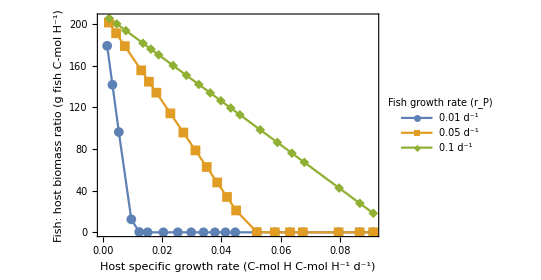

```mathematica
PHGrowthLeg=LineLegend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],  ColorData[97,"ColorList"][[3]]}, {"0.01 d^-1","0.05 d^-1","0.1 d^-1"}, LabelStyle-> {18}, LegendMarkers->Automatic,LegendLabel-> "Fish growth rate (r_P)"];

Legended[ListLinePlot[{PHgrowthrp01Plot,PHgrowthrp05Plot,PHgrowthrp1Plot},PlotMarkers->{Automatic, 10},(*PlotLabel->"Ratio of fish to host interstitial biomass at varying host and fish growth rates",*)ImageSize-> Full, LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 18(*label size*)],  PlotRange->Full,Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0.00005, 0.0001, 0.00015},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Fish: host biomass ratio (g fish C-mol H^-1)",None},{"Host specific growth rate (C-mol H C-mol H^-1 d^-1)",None}}, FrameTicksStyle->Directive[Black,14(*size of ticks*)], FrameStyle->Directive[Black,18](*axis label size*), AspectRatio->0.7(*PlotLegends->{"rp=0.01","rp=0.05","rp=0.1"},PlotMarkers->{Automatic, 6}*)], Placed[PHGrowthLeg,{Right(*left to right position is in the center*),0.8(*top to bottom position*)}]]
```

## Fig. S4: Goldilocks nitrogen effects at different light magnitudes

### Run simulations and format results

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=0;
P0=0;

(*light function values*)
tStartStress=600;
tHigh=30;
(*LHigh=35;*)

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=800;

(*use nested Table to simulate the model with light pulses of different magnitudes and at different levels of Nenv*)

NRangeRuns=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,minGrowth,minSSU,minHSU(*, bleached*)(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*minimum host growth rate: see if growth ever went negative*)
(*evaluate host growth rate at all points from the start of stress to the end of the run (EXCEPT when t is exactly equal to tStartStress and tStartStress +tHigh because at these points one of the HeavisideTheta functions has an argument of 0 which is not evaluated so the growth values are inaccurate) and record the minimum of these values*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

{minGrowth,minSSU,minHSU}(*output*)],

{LHigh, {25, 26, 27}}],(*repeat the above for 3 different LHigh values*)
{Ν,{0.1*10^-7,1*10^-7,2*10^-7,3*10^-7,3.6*10^-7,3.7*10^-7,4*10^-7,5*10^-7,6*10^-7,7.2*10^-7,7.3*10^-7,8*10^-7,9*10^-7,1*10^-6,2*10^-6,2.5*10^-6,2.6*10^-6,3*10^-6,4*10^-6,5*10^-6,5.1*10^-6,6*10^-6}}(*repeat all this for different Nenv*)
];
```

#### Get the results in the correct form to plot

```mathematica
(*transpose the output to change the nested list from {{L1 at N1, L2 at N1, L3 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at L1}, {L2}, {L3}} *)
NseparateL=Transpose[NRangeRuns];
(*lowest light*)
LowL=NseparateL[[1]];
(*mid light*)
MidL=NseparateL[[2]];
(*highest light*)
HighL=NseparateL[[3]];

(*separate each response variable*)
(*low light*)
LowLgrowth=Transpose[LowL][[1]]; (*min host growth*)
LowLSSU=Transpose[LowL][[2]];(*min S SU lim*)
LowLHSU=Transpose[LowL][[3]];(*min H SU lim*)

(*mid light*)
MidLgrowth=Transpose[MidL][[1]]; (*min host growth*)
MidLSSU=Transpose[MidL][[2]];(*min S SU lim*)
MidLHSU=Transpose[MidL][[3]];(*min H SU lim*)

(*high light*)
HighLgrowth=Transpose[HighL][[1]]; (*min host growth*)
HighLSSU=Transpose[HighL][[2]];(*min S SU lim*)
HighLHSU=Transpose[HighL][[3]];(*min H SU lim*)

(*list of Nenv values*)
NVals={0.1*10^-7,1*10^-7,2*10^-7,3*10^-7,3.6*10^-7,3.7*10^-7,4*10^-7,5*10^-7,6*10^-7,7.2*10^-7,7.3*10^-7,8*10^-7,9*10^-7,1*10^-6,2*10^-6,2.5*10^-6,2.6*10^-6,3*10^-6,4*10^-6,5*10^-6,5.1*10^-6,6*10^-6};

(*use Table to get the lists in the form to plot*)
NLightLists=Table[Module[{PlotList},PlotList=Transpose@{NVals,list}; PlotList], {list, {LowLgrowth,LowLSSU,LowLHSU,MidLgrowth,MidLSSU,MidLHSU,HighLgrowth,HighLSSU,HighLHSU}}];
```

### Plot the results

```mathematica
(*line at y=0*)
zeros=ConstantArray[0,Length[NVals]];
zeroLine=Transpose@{NVals,zeros};

paddingS3={{80(*left*),15(*right*)}, {50(*bottom*),10(*top*)}};
(*host growth rate*)
plotS3a=ListLinePlot[{NLightLists[[1]], NLightLists[[4]], NLightLists[[7]], zeroLine},PlotLabel->"a) Minimum host specific growth rate",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[4]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[8]]},Directive[Black, Thickness[0.001]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1 ",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];

(*S SU limitation*)
plotS3c=ListLinePlot[{NLightLists[[2]], NLightLists[[5]], NLightLists[[8]], zeroLine},PlotLabel->"c) Minimum symbiont biomass C-/N-limitation",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[4]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[8]]},Directive[Black, Thickness[0.001]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Ambient nitrogen (mol N L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];

(*H SU limitation*)
plotS3b=ListLinePlot[{NLightLists[[3]], NLightLists[[6]], NLightLists[[9]], zeroLine},PlotLabel->"b) Minimum host biomass C-/N-limitation",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[4]], ColorData[97,"ColorList"][[5]], ColorData[97,"ColorList"][[8]],Directive[Black, Thickness[0.001]](*,Directive[Black, Thin]*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Ambient nitrogen (mol N L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];
```

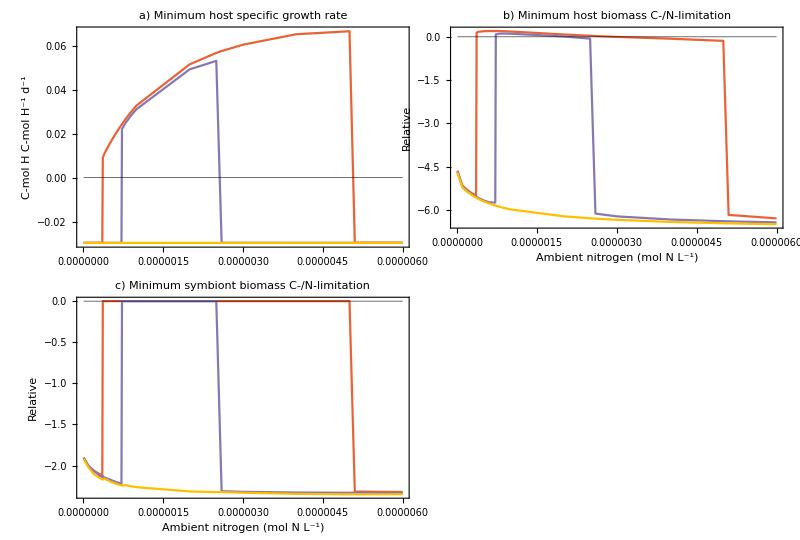

```mathematica
GoldiLLeg=LineLegend[{ColorData[97,"ColorList"][[4]], ColorData[97,"ColorList"][[5]], ColorData[97,"ColorList"][[8]]}, {"40","41","42"},LegendLabel-> "Light pulse magnitude \n(mol photons m^-2 d^-1)",LabelStyle-> {16}];

SGoldiLFig=Legended[GraphicsGrid[{{plotS3a, plotS3b},{plotS3c}}, ImageSize->Full,Spacings->{ {0(*left*),-140(*labels and left col*)(*left to right*)},{0(*top*),0(*middle 2 rows*) (*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*)(*, Alignment-> Bottom*) (*align the grid at the bottom of its frame*)],Placed[GoldiLLeg,(*Bottom*){Right(*left to right position is in the center*), 0.25(*top to bottom position*)}]]
```

## Fig. S5: Goldilocks effects of nitrogen at different levels of prey

### Run simulations and format results

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=0;
P0=0;

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=27;(*light pulse magnitude; this is the highest value used in the above simulations where LHigh was varied*)

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=800; 

(*use nested Table to simulate the model with different levels of prey and at different levels of Nenv*)
NRangeRunsX=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,minGrowth,minSSU,minHSU(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*minimum host growth rate: see if growth ever went negative*)
(*evaluate host growth rate at all points from the start of stress to the end of the run (EXCEPT when t is exactly equal to tStartStress and tStartStress +tHigh because at these points one of the HeavisideTheta functions has an argument of 0 which is not evaluated so the growth values are inaccurate) and record the minimum of these values*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

{minGrowth,minSSU,minHSU}(*record output*)],

{X, {0, 5*10^-8, 1*10^-7}}],(*iterate the above for 3 different prey levels*)
{Ν,{0.1*10^-7, 1*10^-7,2*10^-7,3*10^-7,4*10^-7,5*10^-7,6.1*10^-7,6.2*10^-7,7*10^-7,8*10^-7,9*10^-7,1*10^-6,1.76*10^-6,1.77*10^-6,2*10^-6,2.57*10^-6,2.58*10^-6,3*10^-6,4*10^-6,5*10^-6,6*10^-6}}(*repeat all this for different Nenv; for prey=0 the host bleaches at all Nenv,for prey=5*10^-8 just right range is from 6.2*10^-7 to 1.76*10^-6, for prey=1*10^-7 just right range is from<1*10^-8 to 2.57*10^-6*)
];
```

#### Get the results in the correct form to plot

```mathematica
(*transpose the output to change the nested list from {{X1 at N1, X2 at N1, X3 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at X1}, {X2}, {X3}} *)
NseparateX=Transpose[NRangeRunsX];
(*lowest X*)
LowX=NseparateX[[1]];
(*mid X*)
MidX=NseparateX[[2]];
(*highest X*)
HighX=NseparateX[[3]];

(*separate each response variable*)
(*low X*)
LowXgrowth=Transpose[LowX][[1]]; (*min host growth*)
LowXSSU=Transpose[LowX][[2]];(*min S SU lim*)
LowXHSU=Transpose[LowX][[3]];(*min H SU lim*)

(*mid X*)
MidXgrowth=Transpose[MidX][[1]]; (*min host growth*)
MidXSSU=Transpose[MidX][[2]];(*min S SU lim*)
MidXHSU=Transpose[MidX][[3]];(*min H SU lim*)

(*high X*)
HighXgrowth=Transpose[HighX][[1]]; (*min host growth*)
HighXSSU=Transpose[HighX][[2]];(*min S SU lim*)
HighXHSU=Transpose[HighX][[3]];(*min H SU lim*)

(*list of Nenv values*)
NVals2={0.1*10^-7, 1*10^-7,2*10^-7,3*10^-7,4*10^-7,5*10^-7,6.1*10^-7,6.2*10^-7,7*10^-7,8*10^-7,9*10^-7,1*10^-6,1.76*10^-6,1.77*10^-6,2*10^-6,2.57*10^-6,2.58*10^-6,3*10^-6,4*10^-6,5*10^-6,6*10^-6};

(*use Table to get the lists in the form to plot*)
NPreyLists=Table[Module[{PlotList},PlotList=Transpose@{NVals2,list}; PlotList], {list, {LowXgrowth,LowXSSU,LowXHSU,MidXgrowth,MidXSSU,MidXHSU,HighXgrowth,HighXSSU,HighXHSU}}];
```

### Plot the results

```mathematica
(*line at y=0*)
zeros2=ConstantArray[0,Length[NVals2]];
zeroLine2=Transpose@{NVals2,zeros2};

paddingS4={{80(*left*),15(*right*)}, {50(*bottom*),10(*top*)}};
(*host growth rate*)
plotS4a=ListLinePlot[{NPreyLists[[1]],NPreyLists[[4]], NPreyLists[[7]], zeroLine2},PlotLabel->"a) Minimum host specific growth rate",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[4]]},Directive[Black, Thickness[0.001]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1 ",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];

(*S SU limitation*)
plotS4c=ListLinePlot[{NPreyLists[[2]],NPreyLists[[5]], NPreyLists[[8]], zeroLine2},PlotLabel->"c) Minimum symbiont biomass C-/N-limitation",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[4]]},Directive[Black, Thickness[0.001]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Ambient nitrogen (mol N L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];

(*H SU limitation*)
plotS4b=ListLinePlot[{NPreyLists[[3]],NPreyLists[[6]], NPreyLists[[9]], zeroLine2},PlotLabel->"b) Minimum host biomass C-/N-limitation",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS3,ImageSize->Full,PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], ColorData[97,"ColorList"][[4]],Directive[Black, Thickness[0.001]](*,Directive[Black, Thin]*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Ambient nitrogen (mol N L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio];
```

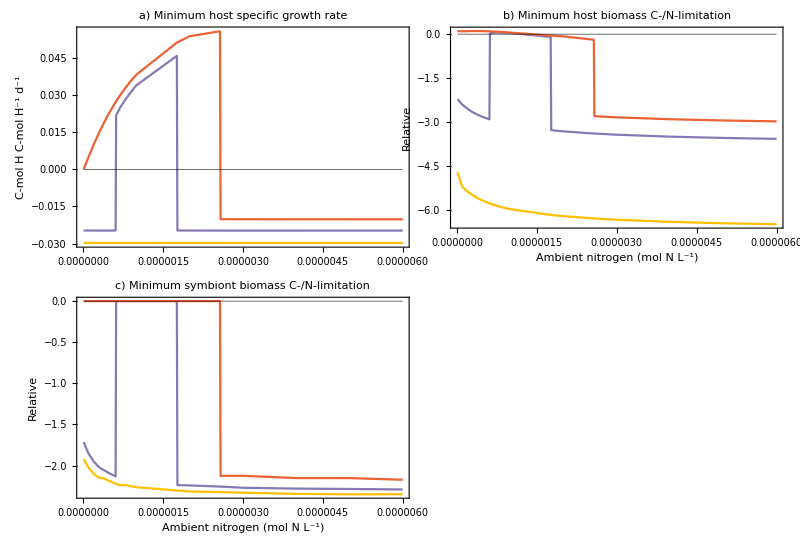

```mathematica
GoldiXLeg=LineLegend[{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], ColorData[97,"ColorList"][[4]]}, {"0","0.5*10^-7","1*10^-7"},LegendLabel-> "Prey (C-mol L^-1)",LabelStyle-> {16}];

SGoldiXFig=Legended[GraphicsGrid[{{plotS4a, plotS4b},{plotS4c}}, ImageSize->Full,Spacings->{ {0(*left*),-140(*labels and left col*)(*left to right*)},{0(*top*),0(*middle 2 rows*) (*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*)(*, Alignment-> Bottom*) (*align the grid at the bottom of its frame*)],Placed[GoldiXLeg,(*Bottom*){Right(*left to right position is in the center*), 0.25(*top to bottom position*)}]]
```

## Fig. S6: Effect of nitrogen in “too low” range on bleached hosts

### Run simulations and format results

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

(*no prey or fish*)
X=0(*1*10^-7*);
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

(*light function parameters*)
tStartStress=600;
LHigh= 25; 
tHigh=30;
tmax=1000; 

(*use Table to simulate the model at different Nenv levels*)
NRuns=Table[
Module[{

(*jX=(jXm X)/(X+KX),*) jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,evalSSU, evalHSU(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations*)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1];
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*min S SU C-lim*)
evalSSU=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol};

(*min H SU C-lim*)
evalHSU=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol} ;

{sol,evalSSU, evalHSU}(*save the whole simulation as output and the time series of S and H SU limitations*)],

{Ν, {1*10^-7,3*10^-7,5*10^-7(*4*10^-6,6*10^-6,8*10^-6*)}}];
```

```mathematica
NSeparate=Transpose[NRuns];
```

```mathematica
Sols=ToExpression[str[NSeparate[[1]]]];
```

```mathematica
HSUev=ToExpression[str[Flatten[NSeparate[[2]]]]];
```

```mathematica
SSUev=ToExpression[str[Flatten[NSeparate[[3]]]]];
```

### plot results

```mathematica
paddingS6={{80(*left*),15(*right*)}, {50(*bottom*),10(*top*)}};

plotS6a=Show[Plot[{Evaluate[{H'[t]/H[t]}/.Sols[[1]]],Evaluate[{H'[t]/H[t]}/.Sols[[2]]],Evaluate[{H'[t]/H[t]}/.Sols[[3]]]},{t,590,tmax},PlotLabel->"a) Host specific growth rate",PlotRange->Full,AxesOrigin->{590,0},LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS6,ImageSize->Full,(*PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[4]]},Directive[Black, Thickness[0.001]]},*)Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1 ",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,tmax},{y,-1000, 1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]] ;


plotS6b=Show[Plot[{HSUev[[1]], HSUev[[2]], HSUev[[3]]},{t,590,tmax},PlotLabel->"b) Host biomass C-/N-limitation",PlotRange->Full,AxesOrigin->{590,0},LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS6,ImageSize->Full,(*PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[4]]},Directive[Black, Thickness[0.001]]},*)Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,tmax},{y,-1000, 1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]] ;

plotS6c=Show[Plot[{SSUev[[1]], SSUev[[2]], SSUev[[3]]},{t,590,tmax},PlotLabel->"c) Symbiont biomass C-/N-limitation",PlotRange->Full,AxesOrigin->{590,0},LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->paddingS6,ImageSize->Full,(*PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[5]], {ColorData[97,"ColorList"][[4]]},Directive[Black, Thickness[0.001]]},*)Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},*)FrameLabel->{{"Relative",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), AspectRatio->1/GoldenRatio],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,tmax},{y,-1000, 1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];
```

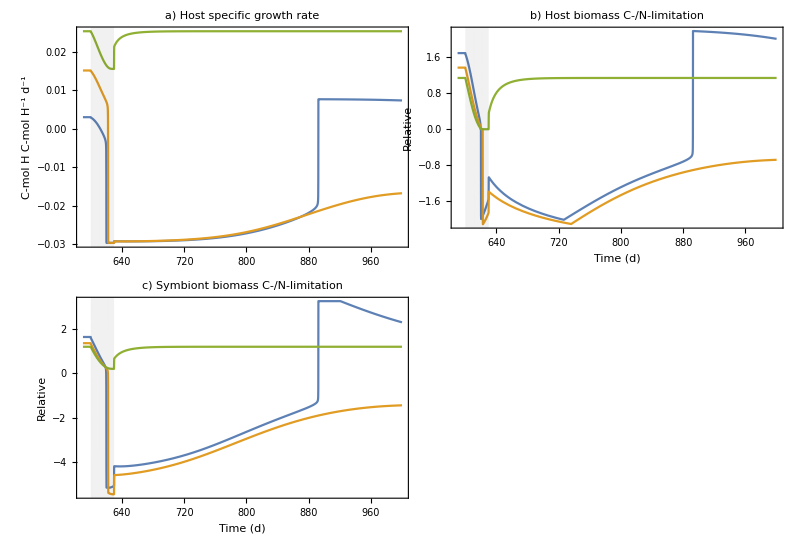

```mathematica
LowNLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]], ColorData[97,"ColorList"][[3]]}, {"1*10^-7","3*10^-7","5*10^-7"},LegendLabel-> "Ambient N (mol L^-1)",LabelStyle-> {16}];

SLowNBleachFig=Legended[GraphicsGrid[{{plotS6a, plotS6b},{plotS6c}}, ImageSize->Full,Spacings->{ {0(*left*),-120(*labels and left col*)(*left to right*)},{0(*top*),0(*middle 2 rows*) (*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*)(*, Alignment-> Bottom*) (*align the grid at the bottom of its frame*)],Placed[LowNLeg,(*Bottom*){Right(*left to right position is in the center*), 0.25(*top to bottom position*)}]]
```

## Fig. S7: Heat maps with higher ambient nitrogen and lower flushing rate

### Run simulations and format results

### Low Nenv, low flushing rate, no fish

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey no fish*)
X=0(*1*10^-7*);
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations at different values of LHigh and tHigh*)
stressRunsnoPnoX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
(*light is L for t<tStartStress and L+LHigh if tStartStress ≤ t < tStartStress+ tHigh and L if t≥ tStartStress+ tHigh *)

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar*LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
(*evaluate host growth rate at all points from the start of stress to the end of the run (EXCEPT when t is exactly equal to tStartStress and tStartStress +tHigh because at these points one of the HeavisideTheta functions has an argument of 0 which is not evaluated so the growth values are inaccurate) and record the minimum of these values*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*save the output*)
Save["stressRunsnoPnoX1",stressRunsnoPnoX1 ]
```

### Low Nenv, low flushing rate, with fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey with fish*)
X=0(*1*10^-7*);
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

stressRunsPnoX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output*)
Save["stressRunsPnoX1",stressRunsPnoX1 ]
```

### Higher Nenv, lower flushing rate, no fish

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey no fish*)
X=0(*1*10^-7*);
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=500(*1660*);
Ν=6*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

stressRunsnoPnoXN =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar*LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
(*evaluate host growth rate at all points from the start of stress to the end of the run (EXCEPT when t is exactly equal to tStartStress and tStartStress +tHigh because at these points one of the HeavisideTheta functions has an argument of 0 which is not evaluated so the growth values are inaccurate) and record the minimum of these values*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
Save["stressRunsnoPnoXN",stressRunsnoPnoXN ]
```

### Higher Nenv, lower flushing rate, with fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey with fish*)
X=0(*1*10^-7*);
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=500(*1660*);
Ν=6*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tStartStress=600;

stressRunsPnoXN =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
Save["stressRunsPnoXN",stressRunsPnoXN]
```

### Format results

```mathematica
(*recover the outputs*)
Get["stressRunsnoPnoX1" ];
Get["stressRunsPnoX1" ];
Get["stressRunsnoPnoXN" ];
Get["stressRunsPnoXN" ];
```

```mathematica
(*say the system only bleached if growth was neg and both SUs were C-limited, recovered if all returned to positive, no stress if all remained positive, mild stress if at least one went negative*)
(*if the min of the three is negative but the max of the three is positive, then at least one is negative*)
makeMatrixS=Table[ Module[{Separate,minGrowthVals,minSSUVals,minHSUVals,growthFinalVals,SSUFinalVals,HSUFinalVals, Vals, Matrix},
Separate=Transpose[Flatten[holdm,1]];
(*select each set of outputs*)
minGrowthVals=Separate[[1]];(* mininimum growth from each simulation is the first element of Separate*)
minSSUVals=Flatten[Separate[[2]]];
minHSUVals=Flatten[Separate[[3]]];
growthFinalVals=Flatten[Separate[[4]]]; (*growth 100 days after stress ends*)
SSUFinalVals=Flatten[Separate[[5]]];
HSUFinalVals=Flatten[Separate[[6]]]; 
Vals=Table[If[minGrowthVals[[num]]>0 && minHSUVals[[num]]≥ 0 && minSSUVals[[num]]≥ 0, 1,If[Min[minGrowthVals[[num]],minHSUVals[[num]],minSSUVals[[num]]]<0  && Max[minGrowthVals[[num]],minHSUVals[[num]],minSSUVals[[num]]]≥ 0, 2, If[ minGrowthVals[[num]]<0&& minHSUVals[[num]]<0&& minSSUVals[[num]]<0&&growthFinalVals[[num]]>0 && HSUFinalVals[[num]]≥ 0&& SSUFinalVals[[num]]≥ 0,3, 4]]],{num, 1,240, 1}];
(*turn the values into a 15x16 matrix: rows are light levels, columns are light durations*)
Matrix=ArrayReshape[Vals, {15, 16}]; (*rows are tHigh's, columns are LHigh's *)
{Matrix}],
{holdm, {stressRunsnoPnoX1,stressRunsPnoX1,stressRunsnoPnoXN,stressRunsPnoXN}}];

(*name the matrices to plot*)
MatrixnoPnoX1=Flatten[makeMatrixS[[1]],1];
MatrixPnoX1=Flatten[makeMatrixS[[2]],1];
MatrixnoPXN=Flatten[makeMatrixS[[3]],1];
MatrixPXN=Flatten[makeMatrixS[[4]],1];
```

### Plot results

```mathematica
padding5={{25(*left*),10(*right*)}, {25(*bottom*),10 (*top*)}};
(*low Nenv*)
plotS7a=MatrixPlot[Reverse[MatrixnoPnoX1], PlotLabel->"a) No fish, N_env=1*10^-7, d=1660",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]}, FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18](*change font size*)] ;

plotS7b=MatrixPlot[Reverse[MatrixPnoX1], PlotLabel->"b) Fish, N_env=1*10^-7, d=1660",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True(*,Mesh->{{1, 2}, {1}}*)(*True*), ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

plotS7c=MatrixPlot[Reverse[MatrixnoPXN], PlotLabel->"c) No fish, N_env=6*10^-7, d=500",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]}, FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18](*change font size*)] ;

plotS7d=MatrixPlot[Reverse[MatrixPXN], PlotLabel->"d) Fish, N_env=6*10^-7, d=500",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;
```

```mathematica
(*make legend*)
heatmapLeg=SwatchLegend[{RGBColor["#55F32C"(*hexadecimal*)], RGBColor["#D8E67D"(*#57D138*)],   RGBColor["#7DB7E6"(*#98C28D*)], RGBColor["#AFB3AE"]},{"Not stressed","Mildly stressed", "Bleached and \n recovered", "Bleached with \n mortality"}, LegendMarkerSize->30];
```

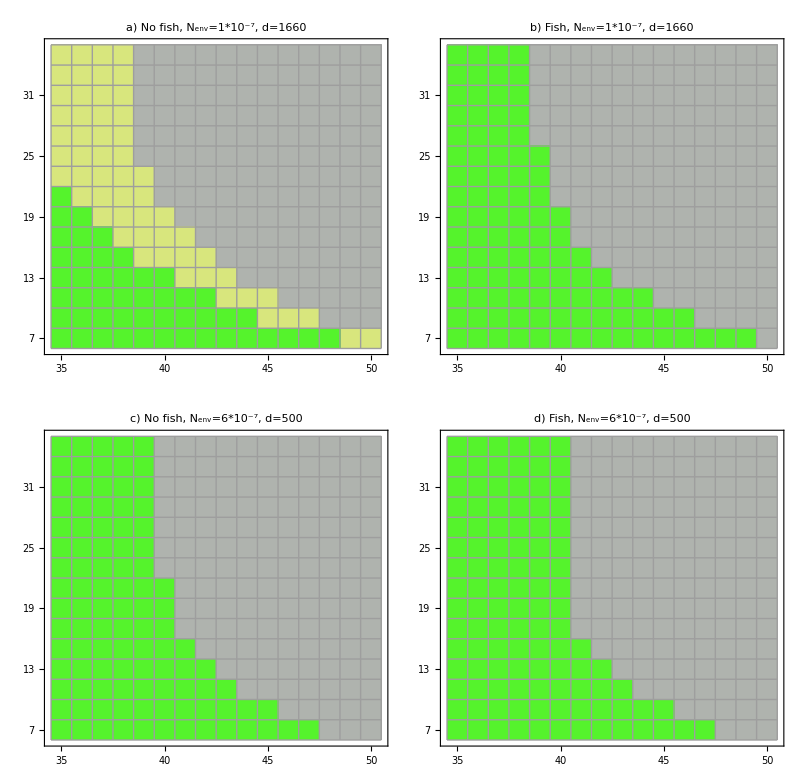
-Graphics-Light pulse duration (d)Light pulse magnitude (mol photons m^-2 d^-1)

```mathematica
SheatmapFig=Legended[Labeled[GraphicsGrid[{{plotS7a, plotS7b}, {plotS7c, plotS7d}}, ImageSize->Full,Spacings->{ {0, -20(*left to right*)},{0,10,10,10(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],{"Light pulse duration (d)","Light pulse magnitude (mol photons m^-2 d^-1)"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 16]],Placed[heatmapLeg,(*Bottom*){1.5,0.8(*x, y position, 0,0 is the lower left corner of the plot*)}]]
```

```mathematica
Export["S_bleach_heatmaps.pdf",SheatmapFig,"PDF"]
```

S_bleach_heatmaps.pdf

## Fig. S8 and S11: Time series of post-bleaching dynamics with and without fish

### Run Simulations

#### No Fish

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*no fish*)
P0=0;

d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

X=1.1*10^-7;

jX=(jXm X)/(X+KX);

(*light function parameters*)
tStartStress=600;
LHigh= 35; 
tHigh=30;
tmax=1000; 

(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

solRecovNoP=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### With Fish

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*with fish*)
P0=kp*(1-α)H0;

d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

X=1.1*10^-7;

jX=(jXm X)/(X+KX);

(*light function parameters*)
tStartStress=600;
LHigh= 35; 
tHigh=30;
tmax=1000; 


(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

solRecovP=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### With fish, carrying capacity depends on interstitial volume

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*constant scaling fish biomass to interstitial volume (from qunatile regression, see Supplementary information on parameterization)*)
kpv = 13.66;

(*with fish*)
P0=kpv*(vi)VH0;

d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

X=1.1*10^-7;

jX=(jXm X)/(X+KX);

(*light function parameters*)
tStartStress=600;
LHigh= 35; 
tHigh=30;
tmax=1000; 

(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kpv*vi*VH-Bp*P)/(kpv*vi*VH))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

solRecovPv=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

### Plot results (Fig. S8: fish carrying capacity scaled to interstitial biomass)

```mathematica
paddingS8={{60(*left*),15(*right*)}, {30(*bottom*),10 (*top*)}};
plotS8a=Show[Plot[{Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"a) Host biomass C-/N-limitation",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Relative",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS8b=Show[Plot[{Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"a) Symbiont biomass C-/N-limitation",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Relative",None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS8c=Show[Plot[{Evaluate@Flatten@{ρC/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{ρC/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"c) Fixed carbon shared with host (ρC)",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol C C-mol S^-1 d^-1",None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS8d=Show[Plot[{Evaluate@Flatten@{ρN/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{ρN/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"d) Nitrogen shared with symbiont (ρN)",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol N C-mol H^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS8e=Show[Plot[{Evaluate@Flatten@{ζ*(1-α)jNw*S/( vi*VH)/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{ζ*(1-α)jNw*S/( vi*VH)/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"e) Waste nitrogen from symbiont",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol N L^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06](*Opacity[0.05, Gray]*)]];

plotS8f=Show[Plot[{Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},PlotLabel->"f) Interstitial nitrogen",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0,{1*10^-7, "1*10^-7"},{2*10^-7,"2*10^-7"},{3*10^-7, "3*10^-7"}},None},{(*None*){500, 550, 600, 650, 700, 750, 800, 850},None}},FrameLabel->{{"mol N L^-1",None}(*\n makes line break*),{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06](*Opacity[0.05, Gray]*)]];

plotS8g=Show[Plot[{Evaluate[{H'[t]/H[t]}/.solRecovNoP ],Evaluate[{H'[t]/H[t]}/.solRecovP]},{t,500,850(*tmax*)},PlotLabel->"g) Host specific growth rate",ImagePadding->paddingS8,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1",None}(*\n makes line break*),{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

recovTSLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]}, {"Fish absent","Fish present"}, LegendMarkerSize->60(*, LegendLayout->{"Row",1}*)];
```

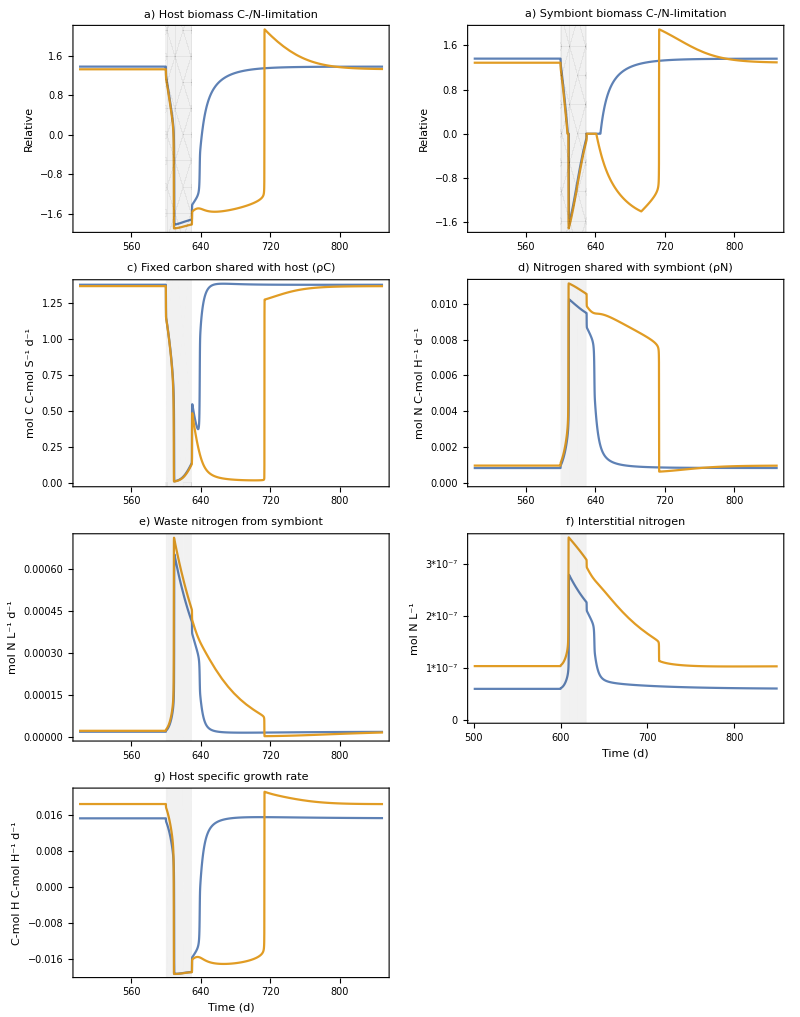

```mathematica
recovTSFig=Legended[GraphicsGrid[{{plotS8a, plotS8b}, {plotS8c,plotS8d},{plotS8e,plotS8f}, {plotS8g}}, ImageSize->Full,Spacings->{ {0(*left*),-30 (*first (leftmost) and second col*)(*left to right*)},{0(*top*),0(*first and second rows*),0 (*second and third*) ,0(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[recovTSLeg,(*Bottom*){0.95, 0.22(*x, y position of legend*)}]]
```

### Plot results (Fig. S11: comparison of fish carrying capacity scaling to interstitial biomass vs. volume)

```mathematica
paddingS9={{80(*left*),15(*right*)}, {30(*bottom*),10 (*top*)}};
plotS9a=Show[Plot[{Evaluate[{H'[t]/H[t]}/.solRecovNoP ],Evaluate[{H'[t]/H[t]}/.solRecovP]},{t,500,850(*tmax*)},PlotLabel->"Fish carrying cap. ∝ (1-α)H",PlotRange->{Full, {-0.021, 0.032}},Epilog->Text[Style["a)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 14(*label size*)],ImagePadding->paddingS9,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Host specific growth rate \n (C-mol H C-mol H^-1 d^-1)",None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9b=Show[Plot[{Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovP }},{t,500,850(*tmax*)},(*PlotLabel->"f) Interstitial nitrogen"*)Epilog->Text[Style["b)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0,{1*10^-7, "1*10^-7"},{2*10^-7,"2*10^-7"},{3*10^-7, "3*10^-7"}},None},{(*None*){500, 550, 600, 650, 700, 750, 800, 850},None}},FrameLabel->{{"Interstitial N (mol N L^-1)",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9c=Show[Plot[{Evaluate[P[t]/.solRecovP], Evaluate[kp*(1-α)*H[t]/.solRecovP]},{t,500,850},(*PlotLabel->"c) Fish biomass"*)PlotRange->{Full, {0, 3.1*10^7}},Epilog->Text[Style["c)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,ImageSize->Full,AxesOrigin->{500,0},PlotStyle->{{ColorData[97,"ColorList"][[2]]}, {ColorData[97,"ColorList"][[2]],Dashed}},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Fish biomass (g)",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)(*, PlotLegends->{"fish biomass", "fish carrying capacity"}*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,0,1*10^10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9d=Show[Plot[{Evaluate[ep*P[t]/( vi*VH[t])/.solRecovP]},{t,500,850},(*PlotLabel->"d) Fish excretion per unit interstitial volume"*)Epilog->Text[Style["d)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,PlotRange->{Full, {0, 0.00025}},ImageSize->Full,AxesOrigin->{500,0},PlotStyle->{{ColorData[97,"ColorList"][[2]]}},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Fish excretion (mol N L^-1 d^-1)",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)(*, PlotLegends->{"fish biomass", "fish carrying capacity"}*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9e=Show[Plot[{Evaluate[{H'[t]/H[t]}/.solRecovNoP ],Evaluate[{H'[t]/H[t]}/.solRecovPv]},{t,500,850(*tmax*)},PlotLabel->"Fish carrying cap. ∝ V_Hi",PlotRange->{Full, {-0.021, 0.032}},Epilog->Text[Style["e)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 14(*label size*)],ImagePadding->paddingS9,ImageSize->Full,AxesOrigin->{500,0}, (*GridLines->{{{tStartStress,Directive[Black]}, {tStartStress+tHigh,Directive[Black]}},{}},*)PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9f=Show[Plot[{Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovNoP },Evaluate@Flatten@{Ni/.addtimetostatevars/.solRecovPv}},{t,500,850(*tmax*)},(*PlotLabel->"f) Interstitial nitrogen"*)Epilog->Text[Style["f)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,PlotRange->Full,ImageSize->Full,AxesOrigin->{500,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]](*, {ColorData[97,"ColorList"][[1]],Dashed}, {ColorData[97,"ColorList"][[2]],Dashed}*)},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0,{1*10^-7, "1*10^-7"},{2*10^-7,"2*10^-7"},{3*10^-7, "3*10^-7"}},None},{(*None*){500, 550, 600, 650, 700, 750, 800, 850},None}},FrameLabel->{{None,None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,500,850},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9g=Show[Plot[{Evaluate[P[t]/.solRecovPv], Evaluate[kpv*vi*VH[t]/.solRecovPv]},{t,500,850},(*PlotLabel->"c) Fish biomass"*)Epilog->Text[Style["g)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,PlotRange->{Full, {0, 3.1*10^7}},(*AxesLabel->{"t"},*)ImageSize->Full,AxesOrigin->{500,0},PlotStyle->{{ColorData[97,"ColorList"][[2]]}, {ColorData[97,"ColorList"][[2]],Dashed}},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)(*, PlotLegends->{"fish biomass", "fish carrying capacity"}*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,0,1*10^10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS9h=Show[Plot[{Evaluate[ep*P[t]/( vi*VH[t])/.solRecovPv]},{t,500,850},(*PlotLabel->"d) Fish excretion per unit interstitial volume"*)Epilog->Text[Style["h)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,PlotRange->{Full, {0, 0.00025}},(*AxesLabel->{"t"},*)ImageSize->Full,AxesOrigin->{500,0},PlotStyle->{{ColorData[97,"ColorList"][[2]]}},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)(*, PlotLegends->{"fish biomass", "fish carrying capacity"}*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];
```

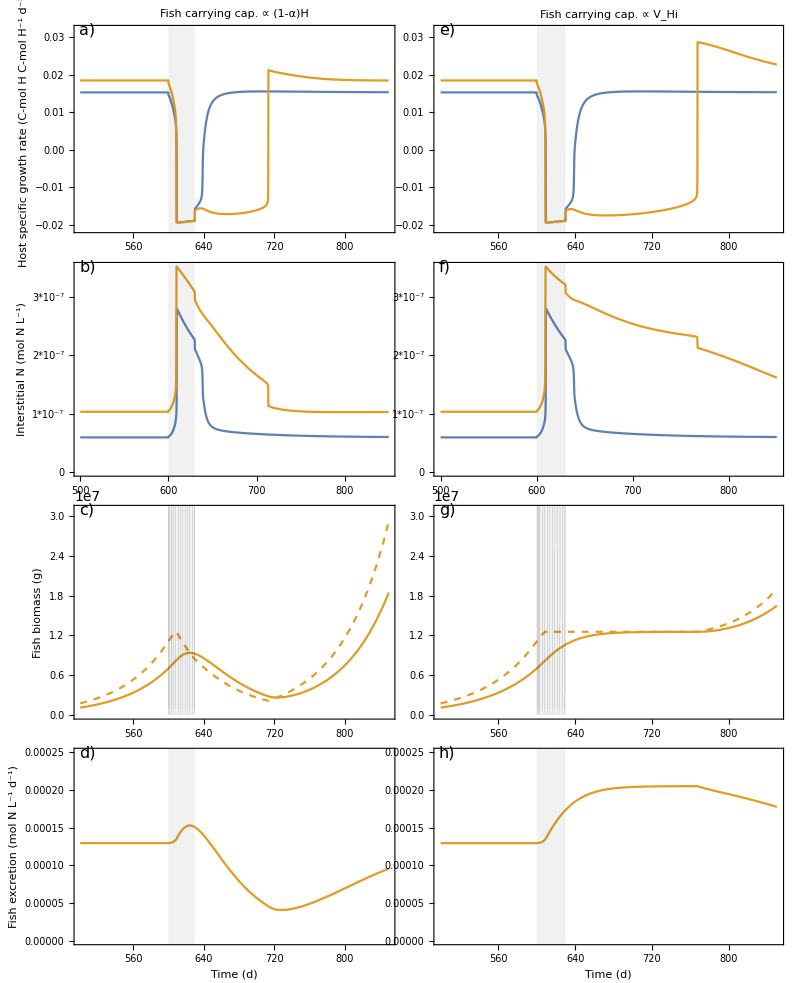

```mathematica
recovPVHLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]], {ColorData[97,"ColorList"][[2]],Dashed}}, {"Fish absent","Fish present", "Fish carrying capacity"}, LegendMarkerSize->60, LegendLayout->{"Row",1}];

recovPVHFig=Legended[GraphicsGrid[{{plotS9a, plotS9e}, {plotS9b,plotS9f},{plotS9c,plotS9g}, {plotS9d, plotS9h}}, ImageSize->Full,Spacings->{ {0(*left*),-60 (*first (leftmost) and second col*)(*left to right*)},{0(*top*),-30(*first and second rows*),-30,-30(*second and third*) (*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[recovPVHLeg,(*Bottom*){0.5, 0(*x, y position of legend*)}]]
```

## Fig. S9: Post-bleaching dynamics when prey is low

### Run simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

X=0.5*10^-7;(*low prey*)
jX=(jXm X)/(X+KX);

tmax=1000; 
tStartStress=600;
tHigh=30;
LHigh=35;

(*use Table to simulate the model with and without fish*)
LowXRuns=
Table[
Module[{

(*jX=(jXm X)/(X+KX),*)(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

{sol}(*save the whole simulation as output*)],

{P0, {0, kp*(1-α)*H0}}];(*repeat once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
```

```mathematica
(*get the state variables*)
LowXnoP=ToExpression[str[Flatten[LowXRuns, 1][[1]]]];
LowXP=ToExpression[str[Flatten[LowXRuns, 1][[2]]]];
```

### Plot results

```mathematica
plotS10a=Show[Plot[{Evaluate[{H'[t]/H[t]}/.LowXnoP],Evaluate[{H'[t]/H[t]}/.LowXP]},{t,400,tmax},PlotLabel->"a) Host specific growth rate",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{400,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS10b=Show[Plot[{Evaluate[{H[t]/VH[t]}/.LowXnoP],Evaluate[{H[t]/VH[t]}/.LowXP]},{t,400,tmax},PlotLabel->"b) Host biomass per unit host volume",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{400,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol H L^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS10c=Show[Plot[{Evaluate[{P[t]}/.LowXnoP],Evaluate[{P[t]}/.LowXP]},{t,400,tmax},PlotLabel->"c) Fish biomass",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{400,0}, PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"g Fish",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1*10^10,1*10^10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plotS10d=Show[Plot[{Evaluate[{Ni[t]}/.LowXnoP],Evaluate[{Ni[t]}/.LowXP]},{t,400,tmax},PlotLabel->"d) Interstitial N",PlotRange->Full,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS9,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{400,0},PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{Ν}},GridLinesStyle->Directive[Black],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol L^-1",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1,1}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];
```

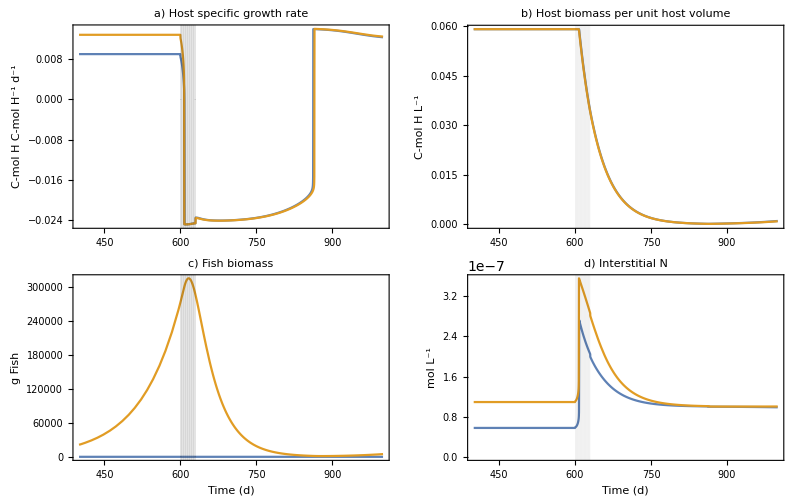

```mathematica
lowXrecovLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]}, {"Fish absent","Fish present"}, LegendMarkerSize->60(*, LegendLayout->{"Row",1}*)];
lowXrecovFig=Legended[GraphicsGrid[{{plotS10a, plotS10b}, {plotS10c,plotS10d}}, ImageSize->Full,Spacings->{ {0(*left*),-30 (*first (leftmost) and second col*)(*left to right*)},{0(*top*),0(*first and second rows*),0 (*second and third*) (*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[lowXrecovLeg,(*Bottom*){1.2, 1.3(*x, y position of legend*)}]]
```

## Fig. S10: Effects of prey and N on recovery time

### Vary prey at lower Nenv

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=1000; 

(*light function parameters*)
tStartStress=600;
tHigh=30;
LHigh=35;

XRecovRuns= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; (* position of these values at which growth is positive, which corresponds to the number of days after stress: if 1st position is pos., then growth was pos. 1 day after stress ended, etc. *)

(*host biomass SU limitation*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the timepoints at which each of these occur *)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];


{RecoveryTime}(*record time to recovery*)],

{P0, {0, kp*(1-α)*H0}}],(*repeat with no fish (P0=0) and with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7}}(*repeat for different levels of prey*)
];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (should have 2 lists total, one for the outputs without fish and one for the outputs with fish*)

(*transpose this to change the nested list from {{P1 at X1, P2 at X1}, {X2}, ...{Xn}} to {{X1, X2, ... Xn at P1}, {P2}} *)
RecovSeparatePX=Transpose[XRecovRuns];
(*prey no fish*)
XRecovNoPX=Flatten[RecovSeparatePX[[1]]];
(*with prey with fish*)
XRecovPX=Flatten[RecovSeparatePX[[2]]];

(*list of X values*)
XVals3={0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7};


(*use Table to get the lists in the form to plot*)
XRecovLists=Table[Module[{PlotList},PlotList=Transpose@{XVals3,list}; PlotList], {list, {XRecovNoPX,XRecovPX}}];
```

### Vary prey at higher Nenv

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=2.5*10^-7 (*1*10^-7 *);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=1100; 

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

XRecovRuns2= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; (* position of these values at which growth is positive, which corresponds to the number of days after stress: if 1st position is pos., then growth was pos. 1 day after stress ended, etc. *)

(*host biomass SU limitation*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the timepoints at which each of these occur*)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];


{RecoveryTime}(*record time to recovery*)],

{P0, {0, kp*(1-α)*H0}}],(*repeat the above with no fish (P0=0) and with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7}}(*repeat for different levels of prey*)
];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (should have 2 lists total, one for the outputs without fish and one for the outputs with fish*)

(*transpose this to change the nested list from {{P1 at X1, P2 at X1}, {X2}, ...{Xn}} to {{X1, X2, ... Xn at P1}, {P2}} *)
RecovSeparatePX2=Transpose[XRecovRuns2];
(*prey no fish*)
XRecovNoPX2=Flatten[RecovSeparatePX2[[1]]];
(*with prey with fish*)
XRecovPX2=Flatten[RecovSeparatePX2[[2]]];

(*list of X values*)
XVals3={0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7};

(*use Table to get the lists in the form to plot*)
XRecovLists2=Table[Module[{PlotList},PlotList=Transpose@{XVals3,list}; PlotList], {list, {XRecovNoPX2,XRecovPX2}}];
```

### Plot the results

```mathematica
paddingS11={{60(*left*),15(*right*)}, {60(*bottom*),10 (*top*)}};

plotS11a=ListLinePlot[{XRecovLists[[1]][[11;; 21]], XRecovLists[[2]][[11;; 21]]},PlotLabel->"a) Effect of prey on recovery, N_env=1*10^-7",PlotRange->{Full, {0, 350}},ImageSize->Full,ImagePadding->paddingS11,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Time in bleached state (d)",None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];

plotS11b=ListLinePlot[{XRecovLists2[[1]][[11;; 21]], XRecovLists2[[2]][[11;; 21]]},PlotLabel->"b) Effect of prey on recovery, N_env=2.5*10^-7",PlotRange->{Full, {0, 350}},ImageSize->Full,ImagePadding->paddingS11,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];
```

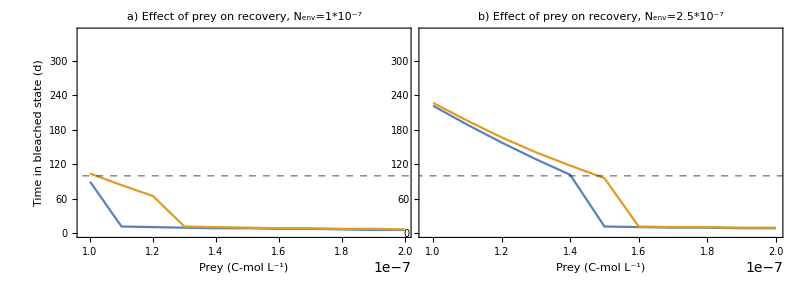

```mathematica
(*make the legend*)
XNRecovLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]}, {"Fish absent","Fish present"}, LegendMarkerSize->40(*, LegendLayout->{"Row",1}*)];

XNRecovFig=Legended[GraphicsGrid[{{plotS11a, plotS11b}}, ImageSize->Full,Spacings->{ {0(*left?*),-150 (*first (leftmost) and second col*)(*left to right*)},{0(*top*),0(*first and second rows*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[XNRecovLeg,(*Bottom*){1.2, 0.85(*x, y positionof legend*)}]]
```

## Fig. S12: Effects of ζ on bleaching

### Run Simulations and format results

#### Run simulations

```mathematica
(*clear parameters that are changing and intermediate values from simulations*)
ClearAll[Ν,X, P0,jX,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey*)
X=(*0*)1*10^-7;
jX=(jXm X)/(X+KX);

(* environment: flow and N level*)
d=1660;
Ν=1*10^-7;

(*jN=(jNm Ν)/(Ν+KN); (* these all need to be within Table[] because Ν is changing*)
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

(*light function parameters: same light pulse as in section 2*)
tStartStress=600;
LHigh=30; 
tHigh=30;

tmax=800;

(*use Table[] to run simulations at different values of zeta and with and without fish*)
zetaRuns=
Table[
Table[
(*everything that is evaluated each iteration needs to be included in Module*)
Module[{

(*jX=(jXm X)/(X+KX),*) jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0^γ, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol(*put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,x_,y_]:=Piecewise[{{0, y<0},{kv*γ *x^(γ-1)*y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H[t], H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

(*simulate the model and call the output sol*)
sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* outputs to save each iteration of Table *)
{sol}],

{P0, {0, kp*(1-α)*H0}}],
{ζ,{1, 0.5, 0.1}}];(* values of zeta tested*)
```

#### Format results

```mathematica
(*transpose this to change the nested list from {{P1 at z1, P2 at z1}, {z2}, {z3}} to {{z1, z2, z3 at P1}, {P2}} *)
SeparateP=Transpose[zetaRuns];
(*no fish*)
zetaRunsNoP=Flatten[SeparateP[[1]], 1];
(*with fish*)
zetaRunsP=Flatten[SeparateP[[2]], 1];

(*no fish, different zetas*)
zeta100=ToExpression[str[zetaRunsNoP[[1]]]];(*zeta=1*)
zeta50=ToExpression[str[zetaRunsNoP[[2]]]];(*zeta=0.5*)
zeta10=ToExpression[str[zetaRunsNoP[[3]]]];(*zeta=0.1*)

(*fish, different zetas*)
zeta100P=ToExpression[str[zetaRunsP[[1]]]];
zeta50P=ToExpression[str[zetaRunsP[[2]]]];
zeta10P=ToExpression[str[zetaRunsP[[3]]]];
```

### Plot results

```mathematica
paddingS12={{80(*left*),15(*right*)}, {30(*bottom*),10 (*top*)}};

(*no fish case*)
(* plot interstitial nitrogen for the three values of zeta *)
plotS12a=Show[Plot[{Evaluate[Ni[t]/.zeta100],Evaluate[Ni[t]/.zeta50],Evaluate[Ni[t]/.zeta10]},{t,500,tmax},PlotLabel->"Fish absent",PlotRange->{Full, {0, 3.6*10^-7}},Epilog->Text[Style["a)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS12,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{500,0},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Interstitial N (mol L^-1)",None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), PlotStyle->{{ColorData[97,"ColorList"][[1]]}, {ColorData[97,"ColorList"][[2]](*,Dashed*)}, {ColorData[97,"ColorList"][[3]]}}],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(* plot host growth rate for the three values of zeta *)
plotS12b=Show[Plot[{Evaluate[H'[t]/H[t]/.zeta100],Evaluate[H'[t]/H[t]/.zeta50],Evaluate[H'[t]/H[t]/.zeta10]},{t,500,tmax},PlotRange->{Full, {-0.021, 0.022}},Epilog->Text[Style["b)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS12,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{500,0},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Host specific growth rate \n (C-mol H C-mol H^-1 d^-1)",None}(*\n makes line break*),{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), PlotStyle->{{ColorData[97,"ColorList"][[1]]}, {ColorData[97,"ColorList"][[2]](*,Dashed*)}, {ColorData[97,"ColorList"][[3]]}}],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(*with fish case*)
(* plot interstitial nitrogen for the three values of zeta  *)
plotS12c=Show[Plot[{Evaluate[Ni[t]/.zeta100P],Evaluate[Ni[t]/.zeta50P],Evaluate[Ni[t]/.zeta10P]},{t,500,tmax},PlotLabel->"Fish present",PlotRange->{Full, {0, 3.6*10^-7}},Epilog->Text[Style["c)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS12,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{500,0},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), PlotStyle->{{ColorData[97,"ColorList"][[1]]}, {ColorData[97,"ColorList"][[2]](*,Dashed*)}, {ColorData[97,"ColorList"][[3]]}}],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(* plot host growth rate for the three values of zeta *)
plotS12d=Show[Plot[{Evaluate[H'[t]/H[t]/.zeta100P],Evaluate[H'[t]/H[t]/.zeta50P],Evaluate[H'[t]/H[t]/.zeta10P]},{t,500,tmax},PlotRange->{Full, {-0.021, 0.022}},Epilog->Text[Style["d)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->paddingS12,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{500,0},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*), PlotStyle->{{ColorData[97,"ColorList"][[1]]}, {ColorData[97,"ColorList"][[2]](*,Dashed*)}, {ColorData[97,"ColorList"][[3]]}}],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-10,10}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];
```

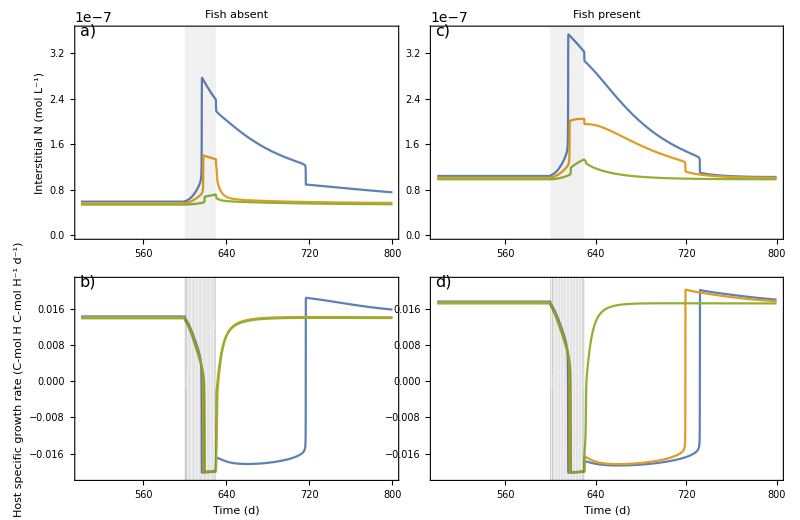

```mathematica
zetaLeg=LineLegend[{ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[2]], ColorData[97,"ColorList"][[1]]}, {"0.1","0.5","1.0"},LegendLabel-> "Fraction of waste N \n available to host",LabelStyle-> {14}];

zetaFig=Legended[GraphicsGrid[{{plotS12a, plotS12c},{plotS12b, plotS12d}}, ImageSize->Full,Spacings->{ {0(*left?*),-80(*labels and left col*)(*left to right*)},{0(*top*),0(*middle 2 rows*) (*labels and bottom*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*)(*, Alignment-> Bottom*) (*align the grid at the bottom of its frame*)],Placed[zetaLeg,(*Bottom*){1.2(*left to right position is in the center*),1(*top to bottom position*)}]]
```